# Theoretical analysis of paradoxical effects in inhibitory-stabilised networks (ISNs) We analyse here a simple network (Wilson-Cowan style) with equal numbers of excitatory and inhibitory neurons. See the accompanying manuscript for details (Sadeh et al. 2017, J Neurosci.).

## Network definition NN defines the number of excitatory, and equal number of inhibitory neurons in the network. The network therefore contains 2NN neurons.

```mathematica
NN:=8;
a:=Flatten[{Table[Indexed[x,i],{i,1,NN}],Table[Indexed[y,i],{i,1,NN}]}];T:=Table[τ,{2NN}];inp:=Table[Indexed[ι,i],{i,1,2NN}];W:=Transpose[ArrayReshape[{Table[we/NN,{2NN},{NN}], Table[-wi/NN,{2NN},{NN}]},{2NN,2NN}]];
J:=ArrayReshape[(W-IdentityMatrix[2NN])/Table[T,{2NN}],{2NN,2NN}]
```

```mathematica
System:=MapThread[Function[{x1,x2},x1==x2],{T Map[#'&,Flatten[a]]+a,Dot[W,a]+inp}]
```

Examine the eigenspectrum of the system Jacobian

```mathematica
J//MatrixForm;
{eigVals,eigVecs}=Eigensystem[J];
eigVals⟦2NN⟧
eigVals⟦2NN⟧/.wi->0
Tr[J]//FullSimplify
```

(-1+we-wi)/τ

(-1+we)/τ

(-16+we-wi)/τ

Make a replacement rule for the trivial eigenvalue

```mathematica
eigValRep:={Evaluate[τ eigVals⟦2NN⟧]->Subscript[λ, 1],wi-we+1->-Subscript[λ, 1]}
```

```mathematica
eigValRep
```

{-1+we-wi→λ_1,1-we+wi→-λ_1}

## Conditions for BIBO stability The network is BIBO stable if all eigenvalues of J have a real part < 0

```mathematica
StabilityCond=Reduce[{eigVals⟦2NN⟧<0,Tr[J]<0,τ>0,we≥0,wi≥0},{we,wi},Reals]//FullSimplify
```

τ>0&&((0≤we<1&&wi≥0)||(we≥1&&1+wi>we))

Examine the constraints for network stability in the absence of inhibition (i.e. wi→0)

```mathematica
StabilityCond/.wi->0//FullSimplify
```

τ>0&&0≤we<1

```mathematica
Reduce[{Tr[J]<0,τ>0},{we},Reals]
```

τ>0&&we<16+wi

## Fixed-point response of the network We obtain the fixed-point response by solving for the point where a’[t]==0.

```mathematica
FPSys:=a/.Solve[System/.τ->0,a]⟦1⟧
```

```mathematica
FPSys/.Table[Indexed[ι,i]->Subscript[ι, inh],{i,NN+1,2NN}]//FullSimplify;
```

```mathematica
FPSys⟦1⟧//FullSimplify
FPSys⟦2NN⟧//FullSimplify
```

1/(8 (-1+we-wi))((7 we-8 (1+wi)) ι_1-we (ι_2+ι_3+ι_4+ι_5+ι_6+ι_7+ι_8)+wi (ι_9+ι_10+ι_11+ι_12+ι_13+ι_14+ι_15+ι_16))

1/(8 (-1+we-wi))(-we (ι_1+ι_2+ι_3+ι_4+ι_5+ι_6+ι_7+ι_8)+wi (ι_9+ι_10+ι_11+ι_12+ι_13+ι_14+ι_15)-8 ι_16+(8 we-7 wi) ι_16)

General form of fixed-point response (Note that j has different ranges for x_j and y_j)

```mathematica
Subscript[x̄, j_]:=(wi Subscript[Σ, i]-we Subscript[Σ, e]+NN Subscript[λ, 1] Subscript[ι, j])/(NN Subscript[λ, 1])
```

```mathematica
Subscript[ȳ, j_]:=(wi Subscript[Σ, i]-we Subscript[Σ, e]+NN Subscript[λ, 1] Subscript[ι, j])/(NN Subscript[λ, 1])
```

```mathematica
Subscript[x̄, 1]
Subscript[x̄, 1]-FPSys⟦1⟧==0/.{Subscript[Σ, e]->Plus@@Table[Indexed[ι,i],{i,1,NN}],Subscript[Σ, i]->Plus@@Table[Indexed[ι,i],{i,NN+1,2NN}],Reverse[eigValRep⟦1⟧]}//Expand//FullSimplify
```

(8 ι_1 λ_1-we Σ_e+wi Σ_i)/(8 λ_1)

ι_1==ι_1

```mathematica
Subscript[ȳ, NN+1]
Subscript[ȳ, NN+1]-FPSys⟦NN+1⟧==0/.{Subscript[Σ, e]->Plus@@Table[Indexed[ι,i],{i,1,NN}],Subscript[Σ, i]->Plus@@Table[Indexed[ι,i],{i,NN+1,2NN}],Reverse[eigValRep⟦1⟧]}//Expand//FullSimplify
```

(8 ι_9 λ_1-we Σ_e+wi Σ_i)/(8 λ_1)

ι_9==ι_9

## Derivative of fixed-point response, under several perturbations Our approach is to find perturbations of several variables, that give rise to a counterintuitive or “paradoxical” response of the network (ref. Tsodyks 1997). For example, driving inhibitory neurons harder has the result of suppressing their activity.

### Perturbation of entire inhibitory population

```mathematica
FullInhDeriv=D[FPSys/.Table[Indexed[ι,i]->Subscript[ι, inh],{i,NN+1,2NN}],Subscript[ι, inh]]//FullSimplify;
```

```mathematica
Reduce[{FullInhDeriv⟦2NN⟧< 0}]//FullSimplify
```

1+wi<we<1||1<we<1+wi

```mathematica
Reduce[{FullInhDeriv⟦2NN⟧< 0,StabilityCond}]//FullSimplify
```

1<we<1+wi&&τ>0

```mathematica
FullInhDeriv⟦2NN⟧
```

(-1+we)/(-1+we-wi)

```mathematica
FullInhDeriv⟦2NN⟧/.eigValRep
```

(-1+we)/λ_1

### Perturbation of single inhibitory neuron

```mathematica
PointDeriv=D[FPSys,Indexed[ι,2NN]]//FullSimplify;
```

```mathematica
Reduce[{PointDeriv⟦2NN⟧<0,StabilityCond}]//FullSimplify
```

1+(7 wi)/8<we<1+wi&&τ>0

```mathematica
PointDeriv⟦2NN⟧//FullSimplify
```

(8-8 we+7 wi)/(8-8 we+8 wi)

```mathematica
1+wi/(NN Subscript[λ, 1])/.Reverse[eigValRep⟦1⟧]//Factor//Expand//FullSimplify
```

(8-8 we+7 wi)/(8-8 we+8 wi)

### Perturbation of inhibitory input to all neurons

```mathematica
GlobalInhDeriv=D[FPSys/.Table[Indexed[ι,i]->Subscript[ι, g],{i,1,2NN}],Subscript[ι, g]]//FullSimplify;
```

```mathematica
Reduce[{GlobalInhDeriv⟦2NN⟧<0,StabilityCond}]//FullSimplify
```

False

```mathematica
GlobalInhDeriv⟦2NN⟧
```

1/(1-we+wi)

### Perturbation of inhibitory weight

```mathematica
FPSysEIInput := FPSys/.Join[Table[Indexed[ι,i]->Subscript[ι, e],{i,1,NN}],Table[Indexed[ι,i]->Subscript[ι, inh],{i,NN+1,2NN}]];InhWeightDeriv=D[FPSysEIInput,wi]//FullSimplify;
```

```mathematica
Reduce[{InhWeightDeriv⟦2NN⟧>0,StabilityCond,we>1,Subscript[ι, e]>0,Subscript[ι, inh]>0},Subscript[ι, inh]]//FullSimplify
```

1<we<1+wi&&ι_e>0&&τ>0&&ι_inh>(we ι_e)/(-1+we)

```mathematica
Reduce[{InhWeightDeriv⟦2NN⟧>0,StabilityCond,we>1,Subscript[ι, e]>0,Subscript[ι, inh]>0,FPSysEIInput⟦2NN⟧>0}]//FullSimplify
```

False

```mathematica
FPSysEIInput⟦1⟧//FullSimplify
FPSysEIInput⟦2NN⟧//FullSimplify
FPSysEIInput⟦1⟧/.eigValRep//FullSimplify
FPSysEIInput⟦2NN⟧/.eigValRep//FullSimplify
```

((1+wi) ι_e-wi ι_inh)/(1-we+wi)

(we ι_e+ι_inh-we ι_inh)/(1-we+wi)

(-(1+wi) ι_e+wi ι_inh)/λ_1

(-we ι_e+(-1+we) ι_inh)/λ_1

```mathematica
InhWeightDeriv⟦1⟧
InhWeightDeriv⟦2NN⟧
InhWeightDeriv⟦1⟧/.eigValRep
InhWeightDeriv⟦2NN⟧/.eigValRep
```

(-we ι_e+(-1+we) ι_inh)/(1-we+wi)^2

(-we ι_e+(-1+we) ι_inh)/(1-we+wi)^2

(-we ι_e+(-1+we) ι_inh)/λ_1^2

(-we ι_e+(-1+we) ι_inh)/λ_1^2

```mathematica
FPSysEIInput⟦1⟧/.{Subscript[ι, e]->Subscript[ι, g],Subscript[ι, inh]->Subscript[ι, g]}//FullSimplify
FPSysEIInput⟦2NN⟧/.{Subscript[ι, e]->Subscript[ι, g],Subscript[ι, inh]->Subscript[ι, g]}//FullSimplify
FPSysEIInput⟦1⟧/.eigValRep/.{Subscript[ι, e]->Subscript[ι, g],Subscript[ι, inh]->Subscript[ι, g]}//FullSimplify
FPSysEIInput⟦2NN⟧/.eigValRep/.{Subscript[ι, e]->Subscript[ι, g],Subscript[ι, inh]->Subscript[ι, g]}//FullSimplify
```

ι_g/(1-we+wi)

ι_g/(1-we+wi)

-ι_g/λ_1

-ι_g/λ_1

```mathematica
FPSysEIInput⟦1⟧/.{Subscript[ι, inh]->we Subscript[ι, e]/(we-1)}//FullSimplify
FPSysEIInput⟦2NN⟧/.{Subscript[ι, inh]->we Subscript[ι, e]/(we-1)}//FullSimplify
```

ι_e/(1-we)

0

## Analysis of general conditions permitting paradoxical response while driving defined portion of inhibitory network Result obtained through observation of dynamics under various NN and various p.

### Conditions for paradoxical response when driving a single inhibitory neuron

```mathematica
GeneralPointParadoxConds[NN_]:={1+(NN-1)wi/NN,1+wi}
```

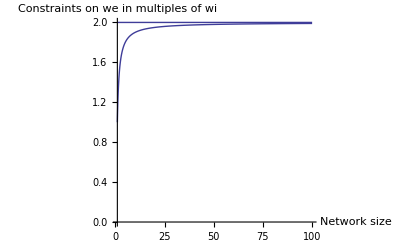

```mathematica
Plot[GeneralPointParadoxConds[x]/.wi->1,{x,1,100},AxesOrigin->{1,0},PlotRange->Full,AxesLabel->{"Network size","Constraints on we in multiples of wi"}]
```

### Conditions for paradoxical response when driving a proportion p of the network Solve the partial derivatives in response to a perturbation, for a given network

```mathematica
PartialDeriv=D[FPSys/.Table[Indexed[ι,i]->Subscript[ι, inh],{i,2NN-2,2NN}],Subscript[ι, inh]]//FullSimplify
```

{-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),-(3 wi)/(8-8 we+8 wi),(8-8 we+5 wi)/(8-8 we+8 wi),(8-8 we+5 wi)/(8-8 we+8 wi),(8-8 we+5 wi)/(8-8 we+8 wi)}

```mathematica
PartialDeriv⟦2NN⟧
```

(8-8 we+5 wi)/(8-8 we+8 wi)

Define a function that returns the analytical estimate for the partial derivative of a stimulation inhibitory neuron

```mathematica
derivPartialStim[numStim_,NN_]:=(NN-we NN+(NN-numStim)wi)/(NN-we NN+wi NN)
```

```mathematica
derivPartialStim[3,NN]//FullSimplify
```

(8-8 we+5 wi)/(8-8 we+8 wi)

```mathematica
1+(3wi)/(NN Subscript[λ, 1])-derivPartialStim[3,NN]/.Reverse[eigValRep⟦1⟧]//FullSimplify
```

0

Define a function that returns the analytical estimate for the partial derivative of a non-stimulated neuron

```mathematica
derivPartialNonStim[numStim_,NN_]:=numStim wi/(NN(we-1-wi))
```

```mathematica
derivPartialNonStim[3,NN]//FullSimplify
```

-(3 wi)/(8-8 we+8 wi)

```mathematica
(3wi)/(NN Subscript[λ, 1])-derivPartialNonStim[3,NN]/.Reverse[eigValRep⟦1⟧]//FullSimplify
```

0

Solve for the proportion of the inhibitory population p that must be perturbed to provoke a paradoxical response

```mathematica
Reduce[{derivPartialStim[p,Num]<0,we>0,wi>0,Num>0,p>0,p≤ Num,StabilityCond},{Num,p},Reals]//FullSimplify
```

1<we<1+wi&&τ>0&&(Num (1-we+wi))/wi<p≤Num

Define a function that analytically determines the minimum proportion of inhibitory neurons that must be perturbed to elicit a paradoxical response, for a given we and wi

```mathematica
propMin[Num_,we_,wi_]:=(Num (1-we+wi))/wi
```

Solve for the parameters that permit a paradoxical response when only a single inhibitory neuron is perturbed

```mathematica
Reduce[{derivPartialStim[1,Num]<0,we>0,wi>0,Num>0,StabilityCond},{Num,wi,wi},Reals]//FullSimplify
```

τ>0&&((we>0&&Num>0&&we≤1&&Num<1&&Num (1-we+wi)<wi)||(we>1&&((0<Num≤1&&1+wi>we)||(Num>1&&we<1+wi&&Num we+wi>Num+Num wi))))

```mathematica
propMin[100,5,20]
```

80

Verify that the simplification for propMin is valid

```mathematica
(-NN Subscript[λ, 1])/wi-propMin[NN,we,wi]/.Reverse[eigValRep⟦1⟧]//FullSimplify
```

0